## Section | Non classical light and quadratures

This chapter introduces nonclassical light: quantum states of the electromagnetic field that cannot be explained by classical physics. We summarize key signatures (sub-Poissonian photon statistics, antibunching, and quadrature squeezing) and show how they appear in squeezed-vacuum and Schrödinger-cat states. We also outline how such states are generated and measured (e.g., parametric down-conversion and homodyne detection). These ideas underpin applications in quantum optics, precision metrology, and quantum information.

#### Key concepts

Single mode quadrature squeezed states

Non-classical properties of squeezed states of light

Homodyne detection

Two-mode squeezed states

### Quadrature squeezing

#### Squeezing definition

If two operators Â and B̂ satisfy the commutation relation , then the Heisenberg uncertainty principle implies the following bound:

A state is called squeezed when one of the following variance criteria is met:

or
both cannot hold otherwise uncertainty principle is violated

For the field quadratures X_1 and X_2 the commutator is , so quadrature squeezing occurs when one quadrature variance drops below the vacuum value.

or

Coherent states (including the vacuum) have equal variances of 1/4 in both quadratures and saturate the uncertainty bound. In phase space this is a circle centered at the mean field. Squeezing deforms the circle into an ellipse: one quadrature variance falls below 1/4 (squeezed) while the orthogonal quadrature increases, keeping the product above the bound. Ideal squeezed states lie on the hyperbola (equality), while realistic states fill the shaded region.

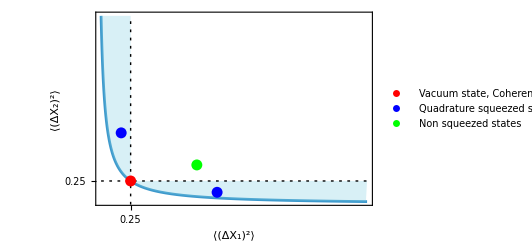

```mathematica
Legended[Show[Plot[1/(16 x),{x,1/32,2},PlotRange->Full,FrameTicks->{{{0.25},None},{{0.25},None}},Epilog->{{Dashing[{0.005,0.01}],Line[{{1/32,0.25},{2,0.25}}]},{Dashing[{0.005,0.01}],Line[{{0.25,0},{0.25,2}}]},{Red,PointSize[0.02],Point[{0.25,0.25}]},{Blue,PointSize[0.02],Point[{0.18,0.76}],Point[{0.89,0.13}]},{Green,PointSize[0.02],Point[{0.74,0.42}]}}],Graphics[{{RGBColor[0.5,0.81,0.89],Opacity[0.3],Polygon[Join[Table[{x,1/(16 x)},{x,1/32,2,0.01}],{{2,0.25},{0.25,0.25},{0.25,2}}  ]]}}],FrameLabel->(Style[#,14]&)/@{"⟨(ΔX_1)^2⟩","⟨(ΔX_2)^2⟩"},Frame->True,ImageSize->500],PointLegend[{Red,Blue,Green},{"Vacuum state, Coherent state","Quadrature squeezed states","Non squeezed states"},LegendFunction->"Panel",LabelStyle->12,LegendMarkerSize->16]]
```

For a coherent state with complex amplitude α, the quadrature means are   and  and :

```mathematica
αc = RandomComplex[]
```

0.803962+0.092867 ⅈ

```mathematica
(QuantumMeasurementOperator[N[#]]@ coherent[αc])["Mean"]& /@ QuadratureOperators[]
```

{0.803962,0.092867}

In phase space this appears as a circle centered at (Re(α), Im(α)):

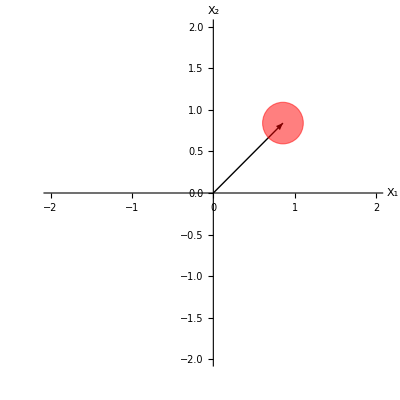

```mathematica
Graphics[
{Arrow[{{0,0},{Re[αc],Im[αc]}}],
EdgeForm[Dashed],Directive[Red],Background->LightBlue,Opacity[0.5],
Disk[{Re[αc],Im[αc]},
Chop[OperatorVariance[coherent[αc],#]&/@QuadratureOperators[]]]},
Axes->True,
AxesOrigin->{0,0},
AxesLabel->(Style[#1,14]&)/@{"X_1","X_2"},
PlotRange->{{-2,2},{-2,2}}]
```

Squeezed states are non-classical because, in the Glauber-Sudarshan P representation representation, a quadrature variance below 1/4 forces P(α) to become negative or more singular in some region of phase space. It is also useful to introduce the angle-dependent quadrature operator X̂(θ) = 1/2(â  e^(-ⅈ θ)+(â)^† e^(ⅈ θ)).

Angle dependent quadrature operator:

```mathematica
Xθ := QuantumOperator[1/2(a ⅇ^(-ⅈ θ)+SuperDagger[a] ⅇ^(ⅈ θ)),"Parameters"->θ];
```

Verify X(0) = X_1 and X(π/2) = X_2:

```mathematica
Thread[{Xθ[0] , Xθ[Pi/2]}==QuadratureOperators[]]
```

{True,True}

Define the squeezing parameter s as s(θ) = 4⟨(ΔX(θ))^2⟩-1. Squeezing is present when, for some angle θ, -1 ≤ s(θ) < 0:

```mathematica
sParameter[ψ_QuantumState,θ_]:= 4 OperatorVariance[ψ,Xθ[θ]]-1
```

### Squeezed operator and squeezed vacuum

The unitary squeeze operator is defined as . It can be viewed as a two-photon analogue of the displacement operator. Here ξ is complex, ξ = r e^(ⅈ θ), and r is the squeeze parameter with 0 ≤ r ≤ ∞.

In the Wolfram Quantum Framework, the squeeze operator can be constructed (optionally specifying the cutoff dimension):

```mathematica
SqueezeOperator[ξ,6]
```

QuantumOperator[…]

The squeeze operator is unitary, so it should satisfy :

```mathematica
FullSimplify[SuperDagger[SqueezeOperator[ξ]]-SqueezeOperator[-ξ]]
```

0

Because we work in a truncated Fock space, some expressions are more numerically stable in a specific operator ordering:

```mathematica
SqueezeOperator[0.3,"Ordering"->"Weak"]["UnitaryQ"]
```

True

Using the Baker-Hausdorff formula we obtain the relations:

Numerically these identities are only approximate because they rely on the commutator [a,a^†] =1 , which is not exact in a truncated Fock space. The squeeze operator is especially sensitive to truncation errors because it involves second-order terms in the annihilation and creation operators. In practice, the Fock cutoff must be larger than for the displacement operator to achieve comparable accuracy.

Construct a squeezed vacuum state :

```mathematica
ξ1 = 0.25 Exp[ⅈ 6π/13];
squeezevacuum = SqueezeOperator[ξ1][];
```

The squeeze operator does not change the mean values of X_1 and X_2:.

```mathematica
(SuperDagger[squeezevacuum]@N[#]@ squeezevacuum)["Scalar"] & /@ QuadratureOperators[]
```

{0,0}

Calculating the variances:

```mathematica
Chop @ OperatorVariance[squeezevacuum,#]& /@ QuadratureOperators[]
```

{0.266204,0.297609}

We see the s-squeezing parameter does take negative values:

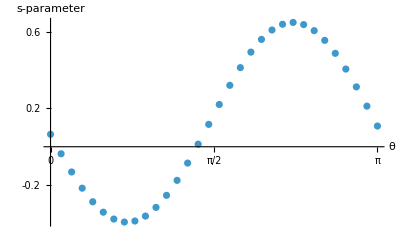

```mathematica
ListPlot[Table[Re[sParameter[squeezevacuum,β]],{β,0,π,0.1}],]
```

Why one of the variances is not going below 0.25?

Using the action of Ŝ on a and a^†, one can derive that:

Verification:

```mathematica
With[{r=Abs[ξ1],θ = Arg[ξ1]},Table[1/4(Cosh[r]^2+Sinh[r]^2-(-1)^m 2Sinh[r]Cosh[r]Cos[θ]),{m,0,1}]]
```

{0.266204,0.297609}

When θ=0, these expressions reduce to . In this case one quadrature is squeezed while the conjugate quadrature is amplified, preserving the uncertainty principle. For θ = 0 the inequality is saturated (the product equals 1/16 = 0.0625). This differs from a coherent state or the vacuum, which also saturate the bound but with equal uncertainties in X_1 and X_2.

Set up a real parameter:

```mathematica
ξ1 = RandomReal[{0,0.6}];
squeezevacuum = SqueezeOperator[ξ1][];
```

Calculate the variances, this time we do get one below 0.25:

```mathematica
variances = (OperatorVariance[squeezevacuum,#]//Chop)& /@ QuadratureOperators[]
```

{0.1391,0.449316}

That coincide with the exponential expressions:

```mathematica
1/4{Exp[-2ξ1],Exp[2ξ1]}
```

{0.1391,0.449316}

Phase-space representation for θ = 0 and θ=π (not to scale). In these cases the squeezing is aligned with the X_1 or X_2 axes, giving axis-aligned error ellipses:

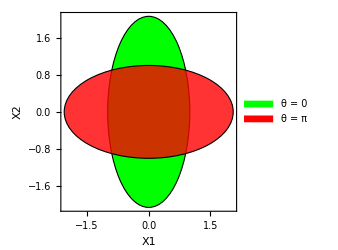

```mathematica
With[{dx =1, dy =variances[[2]]/variances[[1]]//Log}, 
Legended[
Graphics[{
EdgeForm[Dashed],Green,Disk[{0,0},{dx,dy}],
Opacity[0.8],Red,Disk[{0,0},{dy,dx}]},
Axes->True,
Frame->True,
ImageSize->250,
AxesLabel->{"X1","X2"}],
SwatchLegend[{Green,Red},{"θ = 0", "θ = π"}]]]
```

For a general ξ = r e^ⅈθ we define rotated quadratures Y_1 = cos(θ/2)X_1+ sin(θ/2)X_2  and Y_2= -sin(θ/2)X_1+cos(θ/2)X_2 so that the variances are taken along the rotated axes. For these operators the variances are  ⟨Δ Y_1 ⟩^2 = 1/4 e^(-2r) and  ⟨Δ Y_2 ⟩^2 = 1/4 e^(2r). At θ = 0, Y_1 and Y_2 reduce to X_1 and X_2.

Rotated quadrature operators:

```mathematica
YOperators :=( QuantumOperator[#,"Parameters"->θ]& )/@( RotationMatrix[-θ/2].QuadratureOperators[])
```

Setting θ = 0 reduce to the original quadratures:

```mathematica
Through[YOperators[0]] == QuadratureOperators[]
```

True

Squeezed vacuum:

```mathematica
ξ1 = RandomComplex[{0,0.5 ⅇ^(ⅈ π/4)}];
squeezevacuum = SqueezeOperator[ξ1][];
```

Now we do get one quadrature below 0.25:

```mathematica
variances = With[{r = Abs[ξ1], θ1 = Arg[ξ1]}, OperatorVariance[squeezevacuum,#]& /@ Through[YOperators[θ1]]]//Chop
```

{0.187137,0.33398}

That also coincides with the exponential forms as before:

```mathematica
1/4{Exp[-2r],Exp[2r]}/. r->Abs[ξ1]
```

{0.187137,0.33398}

So the earlier plot was only part of the story: a state may be squeezed along a rotated axis, and the squeezing becomes visible only when we measure the correct quadrature.

In phase space the uncertainty ellipses are rotated by θ/2; the dashed lines indicate the Y_1 and Y_2 quadrature axes.

### Other Squeezed states and its properties

#### Squeezed coherent state and displaced squeezed state

A squeezed coherent state is obtained by applying the squeeze operator to a coherent state.

Let’s use a bigger truncation size:

```mathematica
SetFockSpaceSize[80];
```

Set up complex amplitudes:

```mathematica
SeedRandom["Quantum"];
{αcoh,ξ1} = RandomReal[{0.2,1.5},2]Exp[I RandomReal[{0,2π},2]];
```

Build a squeezed coherent state:

```mathematica
squeezeCoh = SqueezeOperator[ξ1]@ DisplacementOperator[αcoh][];
```

The mean photon number has the analytic form:

Mean number of photons from QuantumMeasurementOperator:

```mathematica
(QuantumMeasurementOperator[SuperDagger[a]@a]@squeezeCoh)["Mean"]
```

1.4201

Compare with value from analytical expression:

```mathematica
With[{r=Abs[ξ1],θ = Arg[ξ1]},Abs[αcoh]^2(Cosh[r]^2+Sinh[r]^2)+Sinh[r]^2-2Re[(αcoh^2 Exp[-I θ])]Cosh[r]Sinh[r]]
```

1.4201

A more general state is the displaced squeezed state, defined as |α, ξ ⟩ = D(α) S(ξ)|0⟩. It is not the same as a squeezed coherent state because the displacement and squeeze operators do not commute.

The commutator is therefore nonzero; the following plot shows the matrix of the resulting operator:

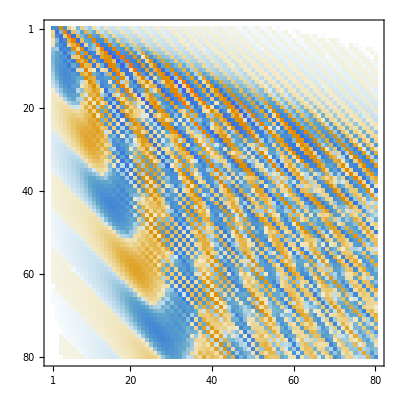

```mathematica
Chop[Commutator[SqueezeOperator[ξ1],DisplacementOperator[αcoh]]["Matrix"]]//MatrixPlot
```

For a displaced squeezed state the mean photon number is:

When r->0 the coherent-state result is recovered; when α → 0 we recover the squeezed-vacuum limit.

Displaced squeezed state:

```mathematica
dispSqueezed = DisplacementOperator[αcoh]@ SqueezeOperator[ξ1][];
```

Mean number of photons comparison:

```mathematica
{(QuantumMeasurementOperator[SuperDagger[a]@a]@ dispSqueezed)["Mean"],Abs[αcoh]^2 +Sinh[Abs[ξ1]]^2}
```

{0.753215,0.753215}

For this state we still have  . This means the uncertainty ellipse keeps its shape for any ξ, while its center is displaced by α.

Variance calculation:

```mathematica
With[{r = Abs[ξ1], θ1 = Arg[ξ1]}, {OperatorVariance[dispSqueezed,#]& /@ Through[YOperators[θ1]]//Chop,1/4{Exp[-2r],Exp[2r]}}]
```

{{0.100791,0.620096},{0.100791,0.620096}}

Phase space representation of the error ellipse:

```mathematica
Module[{θ1=Arg[ξ1],dx ,dy, h=Re[αcoh], k = Im[αcoh]}, 
dx = OperatorVariance[dispSqueezed,YOperators[[1]][θ1]];dy =OperatorVariance[dispSqueezed,YOperators[[2]][θ1]] ;Graphics[{EdgeForm[Thick],Green,
Rotate[Disk[{h,k},{dx,dy}],θ1/2],
Black,Dashed,Line[#+{h,k}&/@Outer[Times,{-dx,dx},{Cos[θ1/2],Sin[θ1/2]}]],Line[#+{h,k}& /@ Outer[Times,{-dy,dy},{-Sin[θ1/2],Cos[θ1/2]}]
],PointSize[0.022],Point[{h,k}],{Red,Dashing[1,0,0],Arrow[{{0,0},{h,k}}],Text["α",{0.24*h,0}+{h,k}/2]}},
Axes->True,Frame->True,ImageSize->Medium,FrameLabel->{"X1","X2"},PlotRange->{{-1,2},{-1,1}},AspectRatio->0.6,ImageSize->400]
]
```

-Graphics-

A very similar picture appears if we plot the Wigner function:

```mathematica
wigner = WignerRepresentation[dispSqueezed,{-5,5},{-5,5}];
```

Plot the Wigner function:

```mathematica
DensityPlot[wigner[x,p],{x,-5,5},{p,-5,5},]
```

-Graphics-

#### Properties of a squeezed vacuum state

For a squeezed vacuum state one can show that the photon-number distribution has support only on even Fock states.

```mathematica
SetFockSpaceSize[41];
```

Random amplitude:

```mathematica
ξ1 = RandomReal[{1,2}]Exp[ⅈ RandomReal[{0,2Pi}]];
```

Squeezed vacuum:

```mathematica
sv = SqueezeOperator[ξ1][];
```

See the photon distribution:

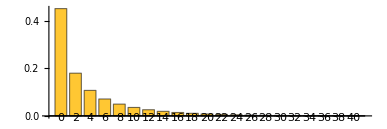

```mathematica
sv["ProbabilityPlot",AspectRatio->1/3]
```

Analytical Fock-basis expansion:

```mathematica
amps =With[{vals = AbsArg[ξ1]}, 1/(√Cosh[vals[[1]]])Table[(-1)^m(√((2m)!))/(2^m  m!)ⅇ^(ⅈ m vals[[2]]) Tanh[vals[[1]]]^m,{m,0,Ceiling[$FockSize/2-1]}]];
```

Check amplitudes equality:

```mathematica
Chop[amps -sv["AmplitudeList"]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

The squeezed vacuum satisfies the Bogoliubov-transformed eigenvalue equation:

Define the linear combination of creation and annihilation operators:

```mathematica
op =(a Cosh[Abs[ξ1]] + ⅇ^(ⅈ Arg[ξ1]) SuperDagger[a] Sinh[Abs[ξ1]]);
```

Indeed the squeezed state is an eigenstate with eigenvalue 0:

```mathematica
Chop[op@sv]
```

0

### Generation of squeezed states

A common way to generate squeezed light is via parametric processes in a nonlinear medium. A pump at frequency ω_P drives the conversion of pump photons into pairs of signal photons with frequency ω = ω_P/2. This is known as degenerate parametric down-conversion.

This process is described by the Hamiltonian:

Here b is the pump mode, a is the signal mode, and  is the second-order susceptibility.

In the undepleted-pump approximation, the pump is treated as a strong classical coherent field |β e^(- ⅈ ω_P t)⟩. Then the operators b and b^† are replaced by the c-numbers e^(- ⅈ ω_P t) and β^* e^(ⅈ ω_P t), and the Hamiltonian reduces to:

where

Set the truncation size:

```mathematica
SetFockSpaceSize[40];
```

Time-independent term:

```mathematica
H0PA = h ω SuperDagger[a]@a;
```

Time-dependent term:

```mathematica
HIPA = ⅈ h (η* a@a ⅇ^(ⅈ Subscript[ω, P] t)-η  (SuperDagger[a]@SuperDagger[a] ⅇ^(-ⅈ Subscript[ω, P] t)));
```

Exponential of the free (noninteracting) part:

```mathematica
U =  MatrixExp[-ⅈ H0PA/h t];
```

Switching to the interaction picture:

```mathematica
HI = QuantumOperator[Simplify[SuperDagger[U]@ HIPA @ U,Element[{h,Subscript[ω, P],t,ω},Reals]],"Parameters"->{Subscript[ω, P],η}];
```

The interaction-picture Hamiltonian is still time dependent, but under the energy-conserving condition ω_P = 2 ω it becomes time independent.

```mathematica
FreeQ[HI[ω,η]["Amplitudes"]//Values,t]
```

False

```mathematica
FreeQ[HI[2ω,η]["Amplitudes"]//Values,t]
```

True

The evolution operator generated by this interaction Hamiltonian has the form of a squeeze operator with ξ = 2 η t. We can verify this by applying it to the vacuum; for the example below we set η = 1:

Comparing the fidelity of states resulting from the application of the operator to the vacuum, let’s consider weak “Ordering” for the numerical SqueezeOperator:

```mathematica
Table[QuantumSimilarity[MatrixExp[-ⅈ HI[2ω,t]/h][],SqueezeOperator[2t,"Ordering"->"Weak"][]],{t,0.1,0.5,0.05}]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.}

Or the default normal order:

```mathematica
Table[QuantumSimilarity[MatrixExp[-ⅈ HI[2ω,t]/h][],SqueezeOperator[2t][]],{t,0.1,0.5,0.05}]
```

{1.,1.,1.,1.,1.,1.,1.,1.,0.999997}

### Detection of squeezed state : Homodyne detection

Using a balanced beam splitter, one can show:

The operator n_3-n_4  corresponds to the photocurrent difference, a directly measurable observable.

Consider an input state where |β⟩ is a coherent local-oscillator state and |ψ⟩ is the signal state:

ϕ is the phase of the complex amplitude β. Define θ = ϕ - π/2; the quadrature at angle θ is . By varying ϕ we scan different quadratures. The corresponding variance is given by the analogous expression .

```mathematica
SetFockSpaceSize[40];
```

Mode operators:

```mathematica
{a1,a2}=Array[AnnihilationOperator[{#}]&,2];
```

Photo-current difference definition:

```mathematica
i34 =ⅈ(SuperDagger[a2]@a1-SuperDagger[a1]@a2);
```

Quadrature at angle θ:

```mathematica
Xθ = QuantumOperator[1/2(a ⅇ^(-ⅈ θ)+ SuperDagger[a] ⅇ^(ⅈ θ)),"Parameters"->θ];
```

We now place a coherent state in the signal port; it must be much weaker than the strong local oscillator.

Signal state:

```mathematica
αc = RandomComplex[];
ψ = coherent[αc];
```

“Strong” local field:

```mathematica
osciAmp = 3;
cohOsci = QuantumState[coherent[osciAmp Exp[I ϕ]]];
```

Total input state (dependent on the local-oscillator phase):

```mathematica
in = QuantumState[QuantumTensorProduct[ψ,cohOsci],"Parameters"->ϕ];
```

Compute the quadratures:

```mathematica
quadratures = Table[{x,(SuperDagger[in[x]]@i34 @ in[x])["Scalar"]/(2osciAmp)//Chop},{x,N@Subdivide[0,2Pi,40]}];//EchoTiming
```

95.5516

Plot the result:

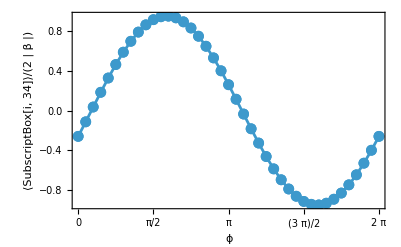

```mathematica
ListLinePlot[quadratures,]
```

For a coherent state, the parameters are easy to read off: X(ϕ = 0) = X(θ = -π/2) = -X_2 and X(ϕ = π/2) = X(θ = 0) = X_1. Thus the real and imaginary parts of α can be obtained directly.

Check the property for the rotated quadrature:

```mathematica
{Xθ[0] == QuadratureOperators[][[1]], Xθ[-π/2] == -QuadratureOperators[][[2]]}
```

{True,True}

Information about the imaginary part:

```mathematica
{-Im[αc],quadratures[[1,2]]}
```

{-0.259025,-0.259025}

Information about the real part:

```mathematica
{Re[αc],quadratures[[Ceiling[(Length@quadratures/4)],2]]}
```

{0.911299,0.911299}

For a displaced squeezed state, the mean of i_34 gives α, while the variance of the photocurrent difference encodes ξ.

Local oscillator:

```mathematica
osciAmp = 4;
cohOsci = QuantumState[coherent[osciAmp Exp[I ϕ]]];
```

Complex squeezing amplitude:

```mathematica
ξ1 = 0.15 Exp[ⅈ RandomReal[{0,π}]];
```

Displaced squeezed state:

```mathematica
ψ = DisplacementOperator[αc]@SqueezeOperator[ξ1][];
```

Total input state:

```mathematica
in = QuantumState[QuantumTensorProduct[ψ,cohOsci],"Parameters"->ϕ];
```

Compute quadrature expectations:

```mathematica
quadratures = Table[{x,(in[x]["Dagger"]@i34 @ in[x])["Scalar"]/(2osciAmp)//Chop},{x,N@Subdivide[0,2Pi,40]}];//EchoTiming
```

75.998

Plot results:

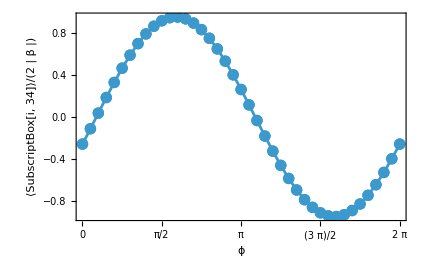

```mathematica
ListLinePlot[quadratures,]
```

Then compute the variances:

```mathematica
variances = Table[{x,OperatorVariance[in[x],N[i34]]/(4 osciAmp^2)//Chop},{x,N@Subdivide[0,2Pi,40]}];//EchoTiming
```

46.7056

Plot the variances:

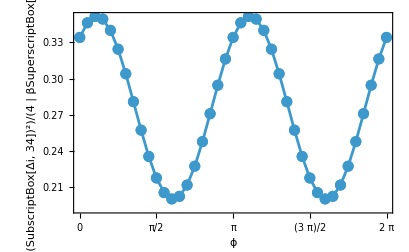

```mathematica
ListLinePlot[variances ,]
```

This yields an estimate of r; accuracy improves as the local oscillator becomes stronger.

Solve for r using the maximum of the variances:

```mathematica
NSolve[{Max[variances[[All,2]]]==1/4Exp[2 r]},r]//First
```

{r→0.170628}

Exact r is used here, so there is some residual error:

```mathematica
Abs[ξ1]
```

0.15

Estimating ϕ can be very accurate because we extract it from a fit to simulated values.

Fit the variances to a sinusoidal form:

```mathematica
nlm =NonlinearModelFit[variances,k Sin[2(ϕ-α)]+c,{k,c,α},ϕ];
```

Phase from the parameters:

```mathematica
2(α /. nlm["BestFitParameters"])-π/2
```

0.694154

Exact ϕ value used:

```mathematica
Arg[ξ1]
```

0.694154

### Schrodinger cat states

Another important class of nonclassical states are superpositions of classical-like states. Consider coherent states with equal amplitude magnitude and a phase difference of π (α and -α); their superposition has the form:

where 𝒩 is a normalization factor , we take α real

When |α| is large, the two coherent components are macroscopically distinguishable and the superposition is called a Schrödinger cat state (by analogy with the 'dead/alive' thought experiment). Schrödinger introduced the idea to highlight tension with the Copenhagen interpretation. In practice, macroscopic superpositions are hard to observe because realistic systems couple to the environment; the resulting decoherence causes the superposition to decohere into a statistical mixture. The state relaxes toward the mixture , and the decay rate grows with |α|. In what follows we focus on the nonclassical signatures of these states.

For the general Schrödinger cat state, ϕ = 0 gives the even cat and ϕ = π gives the odd cat. The case ϕ = π/2 is the Yurke-Stoler state. These three cases are eigenstates of (â)^2 with eigenvalue α^2.

```mathematica
SetFockSpaceSize[21];
```

Let's visualize the photon-number distributions. The even cat state has nonzero amplitudes only on even Fock states:

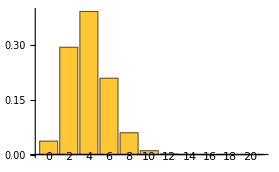

```mathematica
CatState[][2.,0]["ProbabilityPlot"]
```

Eigenstate of a^2 verification ,we can get error in the last term due to truncation:

```mathematica
With[{α=RandomComplex[]},Chop[(a^2)@CatState[][α,0]-α^2 CatState[][α,0]]]
```

0

The odd cat state has nonzero amplitudes only on odd Fock states:

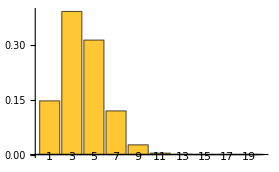

```mathematica
CatState[][2.,π]["ProbabilityPlot"]
```

For the Yurke-Stoler state the photon-number distribution matches that of a coherent state |α⟩, although the amplitudes differ by phase:

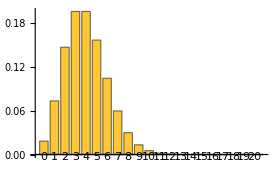

```mathematica
CatState[][2.,π/2]["ProbabilityPlot"]
```

Equal probabilities:

```mathematica
Chop[CatState[][2.,π/2]["ProbabilityList"]-coherent[2.]["ProbabilityList"]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Ratio of amplitudes there is a phase ⅇ^(± ⅈ π /4) for each amplitude, so is not a global phase:

```mathematica
Chop[CatState[][2.,π/2]["AmplitudeList"]/coherent[2.]["AmplitudeList"]]
```

{0.707107+0.707107 ⅈ,0.707107-0.707107 ⅈ,0.707107+0.707107 ⅈ,0.707107-0.707107 ⅈ,0.707107+0.707107 ⅈ,0.707107-0.707107 ⅈ,0.707107+0.707107 ⅈ,0.707107-0.707107 ⅈ,0.707107+0.707107 ⅈ,0.707107-0.707107 ⅈ,0.707107+0.707107 ⅈ,0.707107-0.707107 ⅈ,0.707107+0.707107 ⅈ,0.707107-0.707107 ⅈ,0.707107+0.707107 ⅈ,0.707107-0.707107 ⅈ,0.707107+0.707107 ⅈ,0.707107-0.707107 ⅈ,0.707107+0.707107 ⅈ,0.707107-0.707107 ⅈ,0.707107+0.707107 ⅈ}

Number (amplitude) squeezing is related to the uncertainty relation [n,φ] = ⅈ. A convenient measure of photon statistics is the Mandel Q parameter Q=(⟨(Δn)^2⟩-⟨n⟩)/⟨n⟩. For a state with -1 ≤ Q < 0 the statistics are sub-Poissonian; if Q > 0 they are super-Poissonian, and Q=0 corresponds to Poissonian statistics.

The Mandel Q parameter is > 0 for the even cat state, so it is super-Poissonian statistics for all α. For the odd cat state it is < 0 for all α, showing sub-Poissonian statistics. For the Yurke-Stoler state, Q = 0 because its photon statistics are Poissonian. As |α| becomes large, Q → 0 for both even and odd cat states.

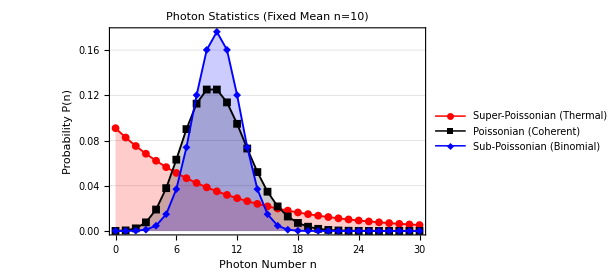

Define Mandel Q-parameter:

```mathematica
MandelQParameter[ψ_QuantumState]:= With[{mean=(ψ["Dagger"]@SuperDagger[a]@a@ψ)["Scalar"]},(OperatorVariance[ψ,SuperDagger[a]@a]- mean)/mean]
```

Calculate the parameter for even cat state, Yurke-Stoler and odd cat state, varying α:

```mathematica
Table[MandelQParameter@CatState[][αc,ϕ],{αc,{0.2,0.5,1.,1.5}},{ϕ,{0,π/2,π}}]//Chop
```

{{0.998934,0,-0.998934},{0.959517,0,-0.959517},{0.551441,0,-0.551441},{0.0999933,0,-0.0999933}}

Even cat states and Yurke-Stoler states exhibit quadrature squeezing (for real α).

Random α:

```mathematica
αc = RandomReal[{0,2}];
```

Quadratures variances for the states:

```mathematica
TableForm[Table[With[{val=Chop@OperatorVariance[CatState[][αc,ϕ],quad]},If[val<0.25,Highlighted[val],val]],{ϕ,{0,π,π/2}},{quad,QuadratureOperators[]}],TableHeadings->]
```

| X_1 | X_2
Even cat | 1.05998 | 0.125126
Odd cat | 1.35525 | 0.420395
Yorke-Stoler | 1.18485 | 0.22778

For the corresponding statistical mixture:

The variances are  and , so there is no squeezing.

For example, for α = 2 define the statistical mixture:

```mathematica
statisticalMixture = 1/2coherent[2.]["MatrixState"]+1/2coherent[-2.]["MatrixState"];
```

Quadrature variances:

```mathematica
With[{m =statisticalMixture["DensityMatrix"]}, Tr[(#@#)["Matrix"].m]- Tr[#["Matrix"].m]^2& /@ QuadratureOperators[]]
```

{4.25,0.25+0. ⅈ}

The Wigner quasi-probability distribution provides a clear contrast between superpositions and mixtures. For the statistical mixture, the Wigner function is just two Gaussian peaks centered at ±α. For the even cat state it displays interference fringes between |α⟩ and |-α⟩, including negative regions that signal nonclassicality. The odd cat and Yurke-Stoler states show similar interference structure.

Wigner function of even cat state:

```mathematica
Block[{wig = WignerRepresentation[CatState[][2,0],{-4.5,4.5},{-4.5,4.5}]},
Plot3D[wig[x,p],{x,-4.5,4.5},{p,-4.5,4.5},
]]
```

-Graphics3D-

Wigner function of statistical mixture:

```mathematica
Block[{wig = WignerRepresentation[statisticalMixture,{-4.5,4.5},{-4.5,4.5}]},
Plot3D[wig[x,p],{x,-4.5,4.5},{p,-4.5,4.5},
]]
```

-Graphics3D-

### Two-mode squeezed vacuum states

We now turn to multimode squeezing, where correlations between modes can produce entanglement. We focus on the two-mode case, defining the two-mode squeeze operator and the two-mode squeezed vacuum:

Note that the two-mode squeeze operator cannot be factored into a product of single-mode squeezers; it therefore creates entangled states with inter-mode correlations.

```mathematica
SetFockSpaceSize[30];
```

Operators for each mode:

```mathematica
{a1,b1}= Array[AnnihilationOperator[{#}]&,2];
```

A convenient way to apply an operator simultaneously to two modes is to use the 'Bend' property:

```mathematica
a1["Bend"] == a1@b1
```

True

Test with creation operator:

```mathematica
SuperDagger[a1]["Bend"][FockState[{0,0}]]//TraditionalForm
```

11

Two mode squeeze vacuum definition:

```mathematica
twoModesqueezeVacuum[ξ_?NumberQ]:= MatrixExp[(ξ* a1@b1-ξ SuperDagger[a1]@SuperDagger[b1]),FockState[{0,0}]]
```

Define the two-mode quadrature operators as:

```mathematica
twomodeX1 := 1/2^(3/2)(a1+SuperDagger[a1]+b1+SuperDagger[b1])
twomodeX2 := 1/(2^(3/2) ⅈ)(a1-SuperDagger[a1]+b1-SuperDagger[b1])
```

One finds that ⟨X_1⟩ = ⟨X_2⟩ = 0:

```mathematica
ξ1 = RandomComplex[];
With[{state = twoModesqueezeVacuum[ξ1]}, (SuperDagger[state]@ # @ state)["Scalar"]& /@ {twomodeX1,twomodeX2}]
```

{0,0}

As in the single-mode case, the variances of X_1 and X_2  are:

Use the two mode quadratures:

```mathematica
OperatorVariance[twoModesqueezeVacuum[ξ1],#]& /@{twomodeX1,twomodeX2}//Chop
```

{0.0698694,1.27091}

Compare with the analytical expression:

```mathematica
With[{r=Abs[ξ1],θ = Arg[ξ1]},Table[1/4(Cosh[r]^2+Sinh[r]^2-(-1)^m 2Sinh[r]Cosh[r]Cos[θ]),{m,0,1}]]
```

{0.0698694,1.27091}

For θ = 0 we recover the single-mode expressions, 1/4 {ⅇ^(-2r), ⅇ^(2r)}:

Use a real parameter, r = 0.3 in this case:

```mathematica
OperatorVariance[twoModesqueezeVacuum[0.3],#]& /@{twomodeX1,twomodeX2}//Chop
```

{0.137203,0.45553}

Compare with the exponentials:

```mathematica
{Exp[-2 0.3],Exp[2 0.3]}/4
```

{0.137203,0.45553}

The two-mode squeezed vacuum can be expanded in the number-state basis as:

Thus the state is entangled with strong photon-number correlations: only |n,n⟩ components appear.

The following plot shows the joint photon-number distribution for a squeeze parameter r = 1.3.

Two mode squeezed vacuum:

```mathematica
s2 = twoModesqueezeVacuum[1.3];
```

Two mode photon distribution, visualizing the correlations:

```mathematica
BarChart3D[ArrayReshape[s2["Probabilities"]//Values,{$FockSize,$FockSize}][[1;;15,1;;15]],]
```

-Graphics3D-

The two modes are symmetric: ⟨n_a⟩ = ⟨n_b⟩ = sinh^2(r).

Calculating the expectations:

```mathematica
With[{state=twoModesqueezeVacuum[ξ1]},(state["Dagger"]@#@state)["Scalar"]& /@{a1["Dagger"]@a1,b1["Dagger"]@b1}]//Chop
```

{0.84078,0.84078}

Hyperbolic sine result:

```mathematica
Sinh[Abs[ξ1]]^2
```

0.84078

From the variances ⟨ (Δn_a)^2⟩= ⟨(Δn_b)^2⟩ = 1/4 sinh^2(r) it follows that both modes exhibit super-Poissonian photon statistics.

Calculate the variances:

```mathematica
With[{state=twoModesqueezeVacuum[ξ1]},OperatorVariance[state,#]& /@{a1["Dagger"]@a1,b1["Dagger"]@b1}]//Chop
```

{1.54769,1.54769}

Hyperbolic sine squared result:

```mathematica
1/4 Sinh[2 Abs[ξ1]]^2
```

1.54769

If we use an entanglement measure such as RenyiEntropy we find that entanglement increases with the squeeze parameter r:

Compute a list of entanglement monotones varying r:

```mathematica
entanglementEntropies = Table[{r,QuantumEntanglementMonotone[twoModesqueezeVacuum[r],"Concurrence"]},{r,0.,1.5,0.05}];
```

Plot the curve, very close to linear behavior for this particular metric:

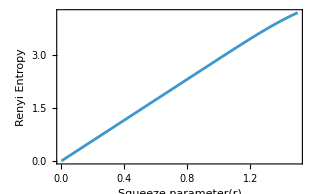

```mathematica
ListLinePlot[entanglementEntropies,Frame->True,FrameLabel->{"Squeeze parameter(r)","Renyi Entropy"},LabelStyle->13]
```

Indeed, it scales linearly with the squeeze parameter:

```mathematica
LinearModelFit[entanglementEntropies,r,r]["RSquared"]
```

0.999603

##### Initialization

Load the Quantum Framework:

```mathematica
Needs["Wolfram`QuantumFramework`"]
```

Load the second quantization tools:

```mathematica
Needs["Wolfram`QuantumFramework`SecondQuantization`"]
```

Useful definitions (for reference):

```mathematica
a := AnnihilationOperator[]
coherent := CoherentState[]["Normalize"];
```

Vocabulary

SqueezeOperator |   | represents a quantum operator that applies squeezing to any 
single mode state
CatState |   | defines a  Schrodinger cat state with arbitrary amplitude and phase

Exercises

Applying on a coherent state with the annihilation operator has no effect on the state itself.04. But consider now the effect of operating on a coherent state with the creation operator a^†. Obtain the normalized state and investigate its properties. Is it a nonclassical state? Check the negative area of the Wigner function varying the value α of the coherent state.

Solution

Show the plot for α = 0.5:

s = (a^†@coherent[0.5])["Normalize"];
wig = WignerRepresentation[s,{-6,6},{-6,6}];

DensityPlot[wig[x,p],{x,-6,6},{p,-6,6},PlotRange->All,PlotPoints->100,ColorFunction->"Rainbow",PlotLegends->Automatic]

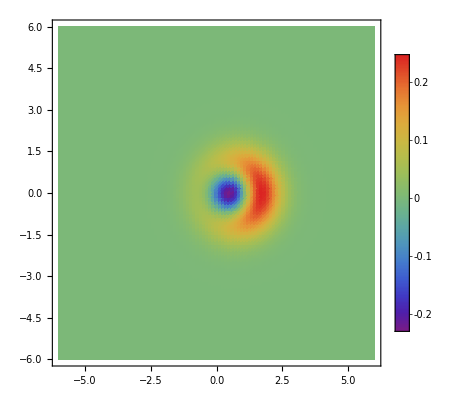

Negative area can be calculated as ∫∫  |W(x,p)| dx dp - 1:

negativeAreas=Table[s = (a^†@coherent[α])["Normalize"];wig = WignerRepresentation[s,{-6,6},{-6,6}];{α,NIntegrate[Abs[wig[x,p]],{x,-6,6},{p,-6,6}]-1},{α,0,1.5,0.1}]//Quiet;

We see there is a negative area but it decreases when α increases, a coherent state with bigger values of α is more “classical”

ListLinePlot[negativeAreas,InterpolationOrder->2,AxesLabel->{"α","Negative Area"}]

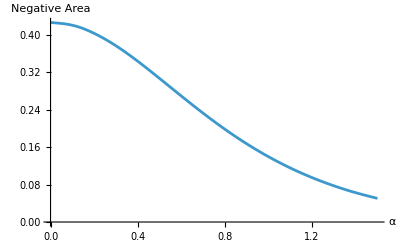

Consider the operators defined as 
K_1 = 1/2 ((a^†)^2+a^2) ,  K_2=1/2ⅈ ((a^†)^2-a^2),  K_3 = 1/2 (a^†a+1/2)
The first two are sometimes referred to as the quadratures of the square of the field. Show that these operators form a closed set under commutation,that is, the commutator of any two yields the third (up to proportionality constant). Obtain the uncertainty product for the operators K1 and K2 and use the coherent states |α⟩.04 to see if they equalize this product.

Solution

Define the operator and calculate the commutator using non-commutative algebra

K1 = 1/2(a^†**a^†+a**a);

K2 = 1/(2ⅈ)(a^†**a^†-a**a);

K3 = 1/2(a^†**a+1/2);

Show [K_1,K_2] = -4 ⅈ K_3:

NonCommutativePolynomialReduce[Commutator[K1,K2]+4ⅈ K3,{Commutator[a,a^†]-1},{a^†,a}][[-1]]

0

Show  [K_2,K_3] =  ⅈ K_1:

NonCommutativePolynomialReduce[Commutator[K2,K3]-ⅈ K1,{Commutator[a,a^†]-1},{a^†,a}][[-1]]

0

Show [K_3,K_1] =  ⅈ K_2:

NonCommutativePolynomialReduce[Commutator[K3,K1]-ⅈ K2,{Commutator[a,a^†]-1},{a^†,a}][[-1]]

0

Using the uncertainty principle for two operators A and B we have ΔA ΔB ≥ 1/2| ⟨ [ A, B] ⟩ |, applying to this case we get Δ K_1 ΔK_2 ≥ 2 ⟨ K_3⟩

K1op = 1/2((a^†)^2+a^2);
K2op = 1/(2ⅈ)((a^†)^2-a^2);
K3op = 1/2(a^†@a+1/2);

Random complex amplitude:

αcoh = RandomReal[{0,2}];

Evaluate the left and right hand side of the inequality:

LHS =√(OperatorVariance[coherent[αcoh],K1op]OperatorVariance[coherent[αcoh],K2op]);

RHS = 2(coherent[αcoh]^†@K3op@coherent[αcoh])["Scalar"];

We see it satisfies the equality:

Chop[LHS-RHS]

0